```mathematica
SetDirectory[NotebookDirectory[]]
Needs["SSS`"]
```

C:\Users\caviness\Documents\Git\SSS-Code\Main

#### Done & To Do

Done: 
★ Rewrite CheckDimension to make it more robust and general, add some checks.  Return value tweaked to give more information.  Calls RecognizeDifferenceRow for actual recognition step.
★ Add checks to ReliableDistances, so it doesn't squawk for disconnected 1-d networks.
★ Write loop to compare different versions of ID summaries, print some interesting cases.  Note that different functions do produce different summaries, these are not unique, but should correctly ID the network.
★ Both 1-D loop and 2-D loop are turning up some probable bugs.  Results of investigation:  It's when CheckDimension is handed a list with ≤2 pts.  Solution:  Write a wrapper function that runs checks before passing them to CheckDimension, etc.
★ GuessDimension:  wrapper function runs needed checks, and grows the sessie if needed to reach agreement for CheckDimension as applied to MaxStateLengthPositions, LeastUsedRulePositions, and DistanceLastPositions, DistanceTally.  Assign a dimension to "Verdict" if warranted (≥ 2 tests agree within 5000 steps).
★ Write function TestForUnusedRules to decide whether to skip this case, and whether a long-jump is possible, once the sessie or the net has been identified (as "Repeating" or otherwise by GuessDimension).

To Do:
★ Write function ImproveInitialState to select a better initial state string, based on the sessie/net ID results provided by CheckDimension, and unchanged tags in "TEvolution". 
★ Add a "NetSummary" field to the sessie object?  [Yes!  Once the dimension has been identified.]

★ Order to do things:  
1. GuessDimension:  Sets "Verdict" if justifiable.  ✓
2. TestForUnusedRules:  Checks that "Verdict" has been assigned, are all rules used in intervals provided by MaxStateLengthPositions, LeastUsedRulePositions, and DistanceLastPositions.  Else long-jump.  ✓
3. ImproveInitialState for cases only we care about.
4. Derive and assign canonical value to "NetSummary".  Add to database.

### Functions that generate lists of integers, and function to ID sessie network

MaxStateLengthPositions, LeastUsedRulePositions, DistanceTally, DistanceLastPositions

#### MaxStateLengthPositions: positions in "Evolution" where a new maximum state string length is reached for the first time

#### LeastUsedRulePositions: positions where the least-used rule was used

#### Note: both of these functions call a filtering function, MergeIntervalsByRulesUsed, which verifies that the same rules are used in each interval between positions in the list, and may discard unimportant positions.

#### DistanceLastPositions: a list containing, for each positive integer n, the position of the last nodes that is n steps from origin on the undirected graph of "Net".

Note: these first three provide lists of numbers based sessie events / network nodes, so as soon as a "Verdict" has been assigned, the CheckDimensions summaries can be used by GuessDimension and TestForUnusedRules.

#### DistanceTally: number of nodes in the undirected graph of "Net" that are no more than 1, 2, 3, ... steps from origin. (SSSAnimate[sss, VertexLabels → "VertexWeight"] gives a related, helpful visualization.)

#### CheckDimensions: accepts a list of "significant" positive integers, returns {"dim"|"exp", n, {k, delay, match}, dt}, where "dim" indicates an n-dimensional network, "exp" a network identified as exponential after n differences. Pattern detection required k-averaging, and a delay before the pattern was established and a difference or ratio match was detected. The difference table dt is provided for human inspection, but in theory this identification (but not the network) could be summarized as {n, dt⟦All, delay;;delay+k⟧} or {"exp", dt⟦All, delay;;delay+k⟧}, respectively. (In fact, only the first element of each row is needed, until the final row.) It is not currently clear whether k and match have any useful meaning in the exponential summary, but both can be reconstructed from the difference table summary.

#### GuessDimension: with appropriate checks, tries all 4 approximative tests by applying CheckDimensions to the lists described above. Sessie is auto-extended to try to reach agreement. Changes "Verdict" if at least 2 tests agree within 5000 steps.

#### TestForUnusedRules:

#### Possible issues & notes:

(1) If dt⟦1,1⟧ == j ≠ 1, there was some initial stuff before the pattern set in.

Solution: If the numbers were provided by either MaxStateLengthPositions or LeastUsedRulePositions, toss out the first j-1 steps of the sessie to generate a network with a difference table in which the first j-1 columns are dropped, and the first row entries are all reduced by subtracting j-1.  If the numbers were produced from the "Net", it's unclear how much of the sessie state strings should be skipped.

(2) Once reliable ID has been made, and initial non-pattern discarded, call TestForUnusedRules (not yet written) to decide whether to skip this case, and whether a long-jump is possible:  affects acceleration.  Also call ImproveInitialState (not yet written), to discard initial or final tagged cells unchanged by the evolution:  only affects sessie display, not the network.  Think carefully about unchanged interior tagged cells:  removing an inert cell might allow a different evolution.

(*) Once we have a network summary...:  Depending on the initial state string, a different network summary might be generated:  how to recognize their equivalence?

Possible solution: Make k alternative summaries, treating by dropping 0, 1, …, k-1 states [as in (1)], sort them (perhaps by last row, then next-to-last, etc.), treat as "canonical" the first in the sorted list.

#### Tested Code:

```mathematica
LeastUsedRulePositions[sss_Association /; KeyExistsQ[sss,"RulesUsed"]] := Module[{ru=sss["RulesUsed"],len,ruletally,least},
len=Length[ru];
ruletally=Tally[ru⟦Round[.1len];;len⟧];      (* skip 10% of rules used, tally the rest *)
least=First@First@SortBy[ruletally,Last];  (* identify the least used rule *)
MergeIntervalsByRulesUsed[Flatten@Position[ru,least],ru]  (* find its occurrences anywhere, merge intervals & return *) 
];
```

```mathematica
LeastUsedRulePositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the least-used rule was applied (least-used in the last 90% of the evolution).  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MaxStateLengthPositions[sss_Association /; KeyExistsQ[sss,"Evolution"]]:=Module[{currmaxlenstringlen,strlens,strt,evollen,evol=sss["Evolution"],b=Boole[sss["Verdict"]==="Repeating"]},
evollen=Length[evol];
strlens=StringLength /@ evol;
currmaxlenstringlen=Min[strlens];
strt=First@First[Position[strlens,currmaxlenstringlen,1]];
Most@
MergeIntervalsByRulesUsed[
Last@Last@Reap[
Do[
If[StringLength[evol⟦n⟧]>currmaxlenstringlen-b,(* if repeating, "≥" *)
Sow[n]; currmaxlenstringlen=StringLength[evol⟦n⟧]
],
{n,strt,evollen}]
],
sss["RulesUsed"]
]
];
```

```mathematica
MaxStateLengthPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the sessie state string reached a new maximum length, starting with the minimum length string -- which hopefully eliminates some initial non-pattern stuff.  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MergeIntervalsByRulesUsed[l0_List,ru_List] := Module[{l=l0,n=Length[l0],rulesused1,rulesused2},
(* Expects a list of interesting integers (l0, defining intervals) and the "RulesUsed" list of some SSS.  Merges any intervals in which fewer different rules were used than in neighboring intervals.
Returns the resulting list, which should be more meaningful than the original one. Give up if length ≤ 2 *) 
While[n>2,
rulesused1=Union[ru⟦l⟦n-2⟧;;l⟦n-1⟧-1⟧];
rulesused2=Union[ru⟦l⟦n-1⟧;;l⟦n⟧-1⟧];
(* If[$debug,Print["rules used:", rulesused1,", ",rulesused2]]; *)
Which[
rulesused1==rulesused2, n--,
SubsetQ[rulesused1,rulesused2], l=Drop[l,{n}];n=Length[l],
SubsetQ[rulesused2,rulesused1], l=Drop[l,{n-2}];n=Length[l],
True,l=Drop[l,{n-1}];n=Length[l]
]
];
l]
```

```mathematica
ReliableDistances[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := Module[{len,net=sss["Net"],odr,z,eins,pos,distances,maxdistance},
If[Length[net]==0,Return[{}]];  (* no network, no distances! *)
eins=Min[Flatten[net/.Rule->List]]; (* call smallest node in net "eins" *)
(* Find the end of last case of the longest run of 0s (or least entry) in the list of remaining outdegrees, after skipping first 10%. *)
len=Length[sss["OutDegreeRemaining"]];
odr=ReplacePart[sss["OutDegreeRemaining"],_?(#<.1len&)->∞];  (* set first 10% = ∞, these will be ignored *)
z = Min[odr];  (* for our purposes, z will be treated as 0, nodes that are as complete as possible have outdegree remaining = z *)
pos=(odr /. {Longest[g___,1],f:Longest[z...,2],h___}:>Length[{g,f}]+Flatten@Position[{h},_?(#≠0&)]);  (* this finds the position of first "untrustworthy" node *) 

(* distances = sss["Distance"]; *)   (* now using undirected graph distances... *)
distances = GraphDistance[UndirectedGraph[sss["Net"]],eins];
(* If[$debug,Print["distances: ",distances]]; *)
maxdistance=Min[distances⟦pos⟧]; (* last distance we'll trust *)
distances /. _?(#>maxdistance&)->-1  (* replace unreliable distances by -1 *)
];
```

```mathematica
DistanceLastPositions[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := 
(* find the position of the last node with (reliable) distance 1, 2, ... *)
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
MergeIntervalsByRulesUsed[
Last[Last[Position[rd,#,{1}]]]& /@ Range[Max[Complement[rd,{∞}]]],
sss["RulesUsed"]
]
]
];
DistanceLastPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions {n_1, n_2, …, n_k} in its causal network, each of which is the last node at the indicated distance from the origin.  Thus n_1 is the node of maximum index which is 1 step away, n_2 the largest that is 2 steps away, etc. But only the final 90% of the network is considered. This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
DistanceTally[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] :=   
(* tally reliable distances, sort, drop the unreliable (-1 & ∞) tally, keep numbers only *) 
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
Accumulate[Last /@ Rest@Sort@DeleteCases[Tally[rd],{∞,_}]]
]
];
DistanceTally::usage = "Takes sss, an already generated sessie object, and returns the list of how many nodes are 0 steps from the origin, how many 1 step away, how many 2 steps away, …. But only the final 90% of the network is considered.";
```

```mathematica
LongestPositiveSubsequence[l_List] := Module[{mx,spl},
spl=SplitBy[l/.ComplexInfinity->∞,0≤#<∞&];
mx=Max[Length/@spl];
First[Select[spl,Length[#]==mx&]]
]
```

```mathematica
Clear[RecognizeDifferenceRow];
RecognizeDifferenceRow[l_List] := Module[{len=Length[l],ptrn,dlay,mtch,k,rats},
For[k=1,k≤len/2,k++,  (* for each possible size moving average run k *)
ptrn=MovingAverage[l,k];
(* Print["ptrn: ",ptrn]; *)
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtch}=(ptrn/.{a:Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}:>{Length[{a}],b}); 
Return[{"dim",{k,dlay,mtch}}]  (* constant row found, needed k-averaging, after dlay *)
];
Off[Divide::infy,Divide::indet];
rats=LongestPositiveSubsequence[Ratios[ptrn]];  (* try ratios instead *)
(* Print["rats: ",rats]; *)
If[MatchQ[rats,{Repeated[_,{0,5}],Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 3 repeated positive ratios between *)
{dlay,mtch}=(rats/.{a:Repeated[_,{0,5}],Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}:>{Length[{a}],b});
On[Divide::infy,Divide::indet];
Return[{"exp",{k,dlay,mtch}}] (* exponential, needed k-averaging, after dlay *)
]
];
{}]  (* {} = failure, {"dim"|"exp", {k,dlay,(diff|ratio)mtch}} = success! *)
```

```mathematica
CheckDimension[l_List]:=Module[{diffsTable={l,Differences[l]},lastrow,ans,k,dlay},
While[Length[lastrow=Last[diffsTable]]≥5, (* stop when rows become too short *)
ans=RecognizeDifferenceRow[lastrow];  (* try to ID this row *)
If[Length[ans]>0, 
(* success, return answer *)
{k,dlay}=Most[ans⟦2⟧];
Return[{
Switch[ans⟦1⟧,
"exp","exp" (* <>ToString[Length[diffsTable]-1] *),
"dim",ToString[Length[diffsTable]-1]<>"D"
],
ans⟦2⟧,
Framed@Grid[diffsTable⟦All,dlay+1;;dlay+k⟧],Grid[diffsTable]}],
(* failure, add another row, try again *)
AppendTo[diffsTable,Differences[Last[diffsTable]]]
]
];
{"failed",Grid[diffsTable]}]
```

```mathematica
Clear[GuessDimension];
SetAttributes[GuessDimension,HoldAll];
GuessDimension[sss0_] := Module[{len,sss,ans,failcnt,vdct,chngd=False},
(* may change the "Verdict" field of the SSS object passed as an argument *)
sss=Evaluate[sss0]; (* local copy to use *)
If[!KeyExistsQ[sss,"Evolution"],Return["Invalid input"]];
If[MatchQ[vdct=sss["Verdict"],"Repeating"|"Dead"], Return[vdct]];
len=Length[sss["RulesUsed"]];
If[len<50,chngd=True; sss=SSSEvolve[sss,50-len]]; (* want ≥50 steps *) If[MatchQ[vdct=sss["Verdict"],"Repeating"|"Dead"], 
If[chngd,sss0=sss]; (* update it if it changed *)
Return[vdct]
];
len=Max[len,50];
ans=CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]};
failcnt=Count[First/@ans,"failed"];
While[len<5000 && failcnt>0, (* try to reach agreement *)
chngd=True;
sss=SSSEvolve[sss,len*failcnt];  (* extend the sss evolution a bit, depending *)
len=Length[sss["RulesUsed"]];
ans=CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]};
failcnt=Count[First/@ans,"failed"];
];
If[failcnt<4,vdct=Complement[First /@ ans,{"failed"}]];
If[Length[vdct]==1,vdct=First[vdct]];
If[len<5000 && failcnt≤2,chngd=True; sss["Verdict"]=vdct]; (* if no more than 2 disagree: at least 2 agree *) 
If[chngd,sss0=sss]; (* update it if changed *)
ans
];
```

```mathematica
TestForAll[rs:<|"Index"->_,"QCode"->_,"RuleSet"->_|>] := Module[{ans}, 
If[Length[ans=TestForConflictingRules[rs]]>0,Return[ans]];
If[Length[ans=TestForNonSoloIdentityRule[rs]]>0,Return[ans]];
If[Length[ans=TestForRenamedRuleSet[rs]]>0,Return[ans]];
If[Length[ans=TestForNonSoloInitialSubstringRule[rs]]>0,Return[ans]];
If[Length[ans=TestForUnbalancedRuleSet[rs]]>0,Return[ans]];
Return[TestForShorteningRuleSet[rs]]
];
```

```mathematica
Clear[TestForUnusedRules];TestForUnusedRules[sss_Association /; KeyExistsQ[sss,"Verdict"]] := Module[{vdct=sss["Verdict"],ru=sss["RulesUsed"],rs=sss["RuleSet"],testresults,summaries,startpos,unjns,reliableQ,rsobj,ndx,qcode,lastruleused,tailweight,newqcode},
If[vdct=="OK",Return[{}]]; (* can't use this test until we have a "Verdict" *)
testresults=If[vdct=="Repeating",{MaxStateLengthPositions[sss],LeastUsedRulePositions[sss]},
{MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss]}];
testresults=Select[testresults,Length[#]≥6&];
summaries=CheckDimension /@ testresults;
If[$debug,Print["testresults: ", testresults]];
If[$debug,Print["summaries: ",summaries]];
startpos=Length[#⟦3,1,1,1⟧]& /@ summaries;
If[$debug,Print["startpos: ",startpos]];
If[$debug,Print["intervals to check for rule usage: ",
MapThread[Partition[#1⟦#2;;⟧,2,1]&,{testresults,startpos}] ]];
If[$debug,Print["rules used in intervals: ",
Map[Part[ru,Span@@#]& ,
MapThread[Partition[#1⟦#2;;⟧,2,1]&,{testresults,startpos}] ,
{2}]]];
unjns=Map[Union[Part[ru,Span@@#]]& ,
MapThread[Partition[#1⟦#2;;⟧,2,1]&,{testresults,startpos}] ,
{2}];
If[$debug,Print["unions of the list of rules used in the intervals: ",unjns]];
reliableQ=(Length[#]>If[vdct=="Repeating",4,8] && Length[Union[#]]==1)&[Flatten[unjns,1]];
If[$debug,Print["reliableQ: ",reliableQ]];
If[!reliableQ,Print["unreliable case: ", rs,": ",summaries]; Return[{}]];
If[$debug,Print["comparing: ",Length[unjns⟦1,1⟧]," to ",Length[rs]]];
If[Length[unjns⟦1,1⟧]==Length[rs],Return[{}]]; (* all rules used *)
rsobj =FromReducedRankRuleSet[rs];
ndx=rsobj["Index"]; qcode=rsobj["QCode"];
lastruleused = Max[unjns⟦1,1⟧];
tailweight=RuleSetWeight[rs⟦lastruleused+1;;⟧];
If[$debug,Print["lastruleused, tailweight: ",{lastruleused,tailweight}]];
If[tailweight==0,Return[FromReducedRankIndex[ndx+1]]]; (* skip one, go on *)
newqcode= StringDrop[qcode,-tailweight]<>"3"<>(StringJoin@@Table["0",{tailweight-1}]);
Return[FromReducedRankQuinaryCode[newqcode]] 
];
```

#### Code still being tested:

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;
Rest /@ 
Map[Last, 
Gather[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs],First[#1]==First[#2]&],
{2}]
];
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i lists the indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
ToReducedNetDifferenceSets[l_List]:=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}],
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]}];
ToReducedNetDifferenceSets::usage ="ToNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns a reduced version in which duplicates or duplicate subsequences are summarized using the format n·{…}.";
```

*** Start here: recognize a row of net difference sets, by (?) "subtracting" with various offsets, identifying case with most 0 entries *)

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets@sss90["Net"]
```

{1·{{1,1,1}},1·{{1,3}},1·{{1,1,1}},1·{{1,1,2}},1·{{3,4}},1·{{1,1,1}},1·{{1,1,3}},1·{{1,1,4}},1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},2·{{1,1,5}},1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},1·{{}},1·{{1,1,1}},8·{{1,1}}}

```mathematica
SetSubtract[1·{{1,3}},1·{{1,1,1}}]
```

{}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets@sss90["Net"]
```

```mathematica
{1·{{1,1,1}},1·{{1,3}},1·{{1,1,1}},1·{{1,1,2}},1·{{3,4}},1·{{1,1,1}},1·{{1,1,3}},1·{{1,1,4}},1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},
2·{{1,1,5}},1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},
3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},1·{{}},1·{{1,1,1}},8·{{1,1}}}
```

```mathematica
Subtract[10,4]
```

6

```mathematica
With[{l = ToReducedNetDifferenceSets@ToNetDifferenceSets@sss90["Net"]},
Print[l[[5+8;;-1]]];
Print[l[[1+8;;-5]]];
Print[SetSubtract[l[[5+8;;-1]], l[[1+8;;-5]]]];
 Print[];
Table[SetSubtract[l[[k;;]], l[[;;-k]]], {k, 2, Length[l]/2}]
 ]
```

{1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},1·{{}},1·{{1,1,1}},8·{{1,1}}}

{1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},2·{{1,1,5}},1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}}}

{0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}}

{{0·{{0,2,∞}},0·{∞},0·{{0,0,1}},0·{{2,3,∞}},0·{∞},0·{{0,0,2}},0·{{0,0,1}},0·{{3,4,∞}},0·{∞},0·{{0,0,3}},1·{{0,0,1}},∞,0·{∞},0·{{0,0,4}},2·{{0,0,1}},∞,0·{∞},0·{{0,0,5}},3·{{0,0,1}},∞,0·{∞},0·{{0,0,6}},4·{{0,0,1}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,1}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,1}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,1}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},0·{{2,3,∞}},0·{{0,0,-1}},0·{∞},0·{{0,0,3}},0·{{3,4,∞}},0·{{0,0,-3}},0·{∞},1·{{0,0,4}},0·{{4,5,∞}},∞,0·{∞},2·{{0,0,5}},0·{{5,6,∞}},∞,0·{∞},3·{{0,0,6}},0·{{6,7,∞}},∞,0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{∞}},{0·{{0,0,1}},0·{{2,1}},0·{{0,0,0}},0·{{0,0,1}},0·{∞},0·{{3,4,∞}},0·{{0,0,-2}},0·{{0,0,0}},1·{∞},0·{{4,5,∞}},0·{{0,0,-3}},∞,2·{∞},0·{{5,6,∞}},0·{{0,0,-4}},∞,3·{∞},0·{{6,7,∞}},0·{{0,0,-5}},∞,4·{∞},0·{{7,8,∞}},0·{{0,0,-6}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-7}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-8}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-9}},0·{{0,0,∞}}},{0·{{2,3,∞}},0·{∞},0·{{0,0,2}},0·{{0,0,2}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},0·{{0,0,3}},0·{{3,4,∞}},0·{∞},0·{{0,0,3}},1·{{0,0,2}},0·{{4,5,∞}},0·{∞},0·{{0,0,4}},2·{{0,0,2}},∞,0·{∞},0·{{0,0,5}},3·{{0,0,2}},∞,0·{∞},0·{{0,0,6}},4·{{0,0,2}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,2}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,2}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,2}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,2}},0·{∞},0·{{3,4,∞}},0·{{0,0,-1}},0·{∞},1·{{0,0,4}},0·{{4,5,∞}},0·{{0,0,-3}},0·{∞},2·{{0,0,5}},0·{{5,6,∞}},∞,0·{∞},3·{{0,0,6}},0·{{6,7,∞}},∞,0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-9,-10}}},{0·{{0,0,3}},0·{{3,2}},0·{{0,0,0}},0·{{0,0,2}},1·{∞},0·{{4,5,∞}},0·{{0,0,-2}},0·{{0,0,1}},2·{∞},0·{{5,6,∞}},0·{{0,0,-3}},∞,3·{∞},0·{{6,7,∞}},0·{{0,0,-4}},∞,4·{∞},0·{{7,8,∞}},0·{{0,0,-5}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-6}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-7}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-8}},1·{{0,0,∞}}},{0·{{3,4,∞}},0·{∞},0·{{0,0,3}},1·{{0,0,3}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},1·{{0,0,4}},0·{{4,5,∞}},0·{∞},0·{{0,0,4}},2·{{0,0,3}},0·{{5,6,∞}},0·{∞},0·{{0,0,5}},3·{{0,0,3}},∞,0·{∞},0·{{0,0,6}},4·{{0,0,3}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,3}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,3}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,3}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,3}},1·{∞},0·{{4,5,∞}},0·{{0,0,-1}},0·{∞},2·{{0,0,5}},0·{{5,6,∞}},0·{{0,0,-3}},0·{∞},3·{{0,0,6}},0·{{6,7,∞}},∞,0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-8,-9}}},{1·{{0,0,4}},0·{{4,3}},0·{{0,0,0}},0·{{0,0,3}},2·{∞},0·{{5,6,∞}},0·{{0,0,-2}},0·{{0,0,2}},3·{∞},0·{{6,7,∞}},0·{{0,0,-3}},∞,4·{∞},0·{{7,8,∞}},0·{{0,0,-4}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-5}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-6}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-7}},2·{{0,0,∞}}},{0·{{4,5,∞}},0·{∞},0·{{0,0,4}},2·{{0,0,4}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},2·{{0,0,5}},0·{{5,6,∞}},0·{∞},0·{{0,0,5}},3·{{0,0,4}},0·{{6,7,∞}},0·{∞},0·{{0,0,6}},4·{{0,0,4}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,4}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,4}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,4}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,4}},2·{∞},0·{{5,6,∞}},0·{{0,0,-1}},0·{∞},3·{{0,0,6}},0·{{6,7,∞}},0·{{0,0,-3}},0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-7,-8}}},{2·{{0,0,5}},0·{{5,4}},0·{{0,0,0}},0·{{0,0,4}},3·{∞},0·{{6,7,∞}},0·{{0,0,-2}},0·{{0,0,3}},4·{∞},0·{{7,8,∞}},0·{{0,0,-3}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-4}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-5}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-6}},3·{{0,0,∞}}},{0·{{5,6,∞}},0·{∞},0·{{0,0,5}},3·{{0,0,5}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},3·{{0,0,6}},0·{{6,7,∞}},0·{∞},0·{{0,0,6}},4·{{0,0,5}},0·{{7,8,∞}},0·{∞},0·{{0,0,7}},5·{{0,0,5}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,5}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,5}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,5}},3·{∞},0·{{6,7,∞}},0·{{0,0,-1}},0·{∞},4·{{0,0,7}},0·{{7,8,∞}},0·{{0,0,-3}},0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-6,-7}}}}

```mathematica
Clear[SetSubtract];
SetSubtract[s2:{___Integer},s1:{___Integer}] := Module[{len1,len2},
If[(len1=Length[s1])<(len2=Length[s2]),∞,Join[s2-s1⟦1;;len2⟧,Table[∞,len1-len2]]]];
SetSubtract[(n2_Integer)·(s2:{{___Integer}..}),(n1_Integer)·(s1:{{___Integer}..})] := Module[{len1,len2},
Which[
n1>n2,∞,
(len1=Length[s1])<(len2=Length[s2]),∞,
True,(n2-n1)·Join[SetSubtract[s2,s1⟦1;;len2⟧],Table[∞,len1-len2]]
]];
SetSubtract[l2_List,l1_List] := 
If[Length[l1]==Length[l2],MapThread[SetSubtract,{l2,l1}]];
SetSubtract::usage="SetSubtract[s1,s2] or SetSubtract[n1·s1,n2·s2] performs a strange sort of 'set subtraction', in which elements of s2 are subtracted in order from the corresponding elements of s1, if the set sizes are the same, so SetSubtract[{1,4,9},{1,2,3}] gives {0,2,6}.  If s1 is longer than s2, the value ∞ is returned, if s2 is longer than s1, elements are subtracted until they run out, and the remaining subtractions return ∞. If n1>n2, the difference is given in the response, otherwise the entire expression returns ∞.";
```

```mathematica
SetSubtract[{1,2,3},{1,2,3,5}]
```

{0,0,0,∞}

```mathematica
SetSubtract[{1,2,3},{1,2}]
```

∞

```mathematica
SetSubtract[3·{{1,2,4}},1·{{1,2,3}}]
```

2·{{0,0,1}}

```mathematica
SetSubtract[{1,3,7},{1,2,3}]
```

{0,1,4}

```mathematica
With[{l = ToNetDifferenceSets[sss1a["Net"]]},
 Table[SetSubtract[l[[k ;;]], l[[;; -k]]], {k, 2, Length[l]/2}]
 ]
```

{{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞},{{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞}}

```mathematica
First@MaximalBy[MapIndexed[{Count[#1,0,∞],First@#2,#1}&,%377,1],First]
```

{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}}

```mathematica
With[{l = ToNetDifferenceSets[sss1a["Net"]]},
 Table[SetSubtract[l[[k ;;]], l[[;; -k]]], {k, 2, Length[l]/2}]
 ]
```

```mathematica
MapIndexed[{Count[#1,0,∞],First@#2,#1}&,%240,1]
```

{{0,1,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}},{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},{0,3,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}},{7,4,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},{0,5,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}},{6,6,{{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},{0,7,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}}}

```mathematica
First@MaximalBy[MapIndexed[{Count[#1,0,∞],First@#2,#1}&,%240,1],First]
```

{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}}

```mathematica
Count[{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},_?AtomQ,∞]
```

8

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}],
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
}]]
```

{7·{{0},{}},1·{{0}}}

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}]]
```

{7·{{0},{}},{0}}

```mathematica
idMatch[{x___,(reps_Integer)·(match_List),z___}] := {Length[{x}],reps,match,Length[{z}]};
```

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}]] // idMatch
```

{0,7,{{0},{}},1}

```mathematica
RecognizeNet[sss_Association /; KeyExistsQ[sss,"Net"]] := 
Module[{netdiffs=ToNetDifferenceSets[sss["Net"]],
```

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequencePosition[l,
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]},Overlaps->False
]
]
```

{{1,14}}

```mathematica
RecognizeNetDifferences[l_List] := Module[{tbl,offst,cnt,ptrn,ttl,dlay,repcnt,mtch,xcs},
(* table of set differences for all offsets *)
tbl=Table[SetSubtract[l[[k;;]],l[[;;-k]]],{k,2,Length[l]/2}];
(* find count, offset and matched pattern for the best one = most 0s *)
{cnt,offst,ptrn}=First@MaximalBy[MapIndexed[{Count[#1,0,∞],First@#2,#1}&,tbl,1],First];
Print[{cnt,offst,ptrn}];
ttl=Count[ptrn,_?AtomQ,∞]; (* maximum number of 0s possible *)
If[cnt/ttl≥0.9 , (* covers 90% of the cases *)

{dlay,repcnt,mtch,xcs}=idMatch@SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}] ;

Print[{dlay,repcnt,mtch,xcs}];
Return[{ToString[100*cnt/ttl]<>"%",{offst,dlay,repcnt,mtch,xcs}}]  (* after dlay *)
]];
RecognizeNetDifferences@ToNetDifferenceSets[sss1a["Net"]]
```

{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}}

{0,8,{{1},{}},1}

{100%,{2,0,8,{{1},{}},1}}

```mathematica
RecognizeNetDifferences[l_List] := Module[{tbl,offst,cnt,ptrn,ttl,dlay,repcnt,mtch,xcs},
(* table of set differences for all offsets *)
tbl=Table[SetSubtract[l[[k;;]],l[[;;-k]]],{k,2,Length[l]/2}];
(* find count, offset and matched pattern for the best one = most 0s *)
{cnt,offst,ptrn}=First@MaximalBy[MapIndexed[{Count[#1,_?NonNegative,∞],First@#2,#1}&,tbl,1],First];
Print[{cnt,offst,ptrn}];
ttl=Count[ptrn,_?AtomQ,∞]; (* maximum number of 0s possible *)
If[cnt/ttl≥0.9 , (* covers 90% of the cases *)

{dlay,repcnt,mtch,xcs}=idMatch@SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}] ;

Print[{dlay,repcnt,mtch,xcs}];
Return[{ToString[100.*cnt/ttl]<>"%",{offst,dlay,repcnt,mtch,xcs}}]  (* after dlay *)
]];
RecognizeNetDifferences@ToReducedNetDifferenceSets@ToNetDifferenceSets[sss90["Net"]]
```

{135,4,{0·{{2,3,∞}},0·{∞},0·{{0,0,2}},0·{{0,0,2}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}}}

{0,1,{{1,1,1}},38}

{103.846%,{4,0,1,{{1,1,1}},38}}

```mathematica
With[{ptrn={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
MatchQ[ptrn,{Repeated[__,{0,5}],Longest[Repeated[b__,{5,∞}]],Repeated[__,{0,3}]}]
]
```

True

```mathematica
RecognizeNetSetDifferenceRow[l:((_List)..)] := Module[{len=Length[l],ptrn,dlay,mtch,k},

For[k=1,k≤len/2,k++,  (* for each possible offset size k *)
ptrn=MovingAverage[l,k];
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtch}=(ptrn/.{a:Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}:>{Length[{a}],b}); 
Return[{"dim",{k,dlay,mtch}}]  (* dimension k, after dlay *)
];
];
{}]  (* {} = failure, {"dim", {k,dlay,(diff|ratio)mtch}} = success! *)
```

Clear[SubtractSetLists];
SubtractSetLists[s1_List, s2_List] := Module[{len1, len2},
   MapThread[If[(len1 = Length[#1]) < (len2 = Length[#2]), ∞, Join[#2 - #1[[1 ;; len2]], Table[∞, len1 - len2]]] &, {s1, s2}]
   ];

With[{l = ToNetDifferenceSets[sss1a["Net"]]},
 Table[SubtractSetLists[l[[k ;;]], l[[;; -k]]], {k, 2, Length[l]/2}]
 ]

{{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}},{{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}}

```mathematica
Count[#,0,∞]& /@ %219
```

{0,8,0,7,0,6,0}

### Examples of usage



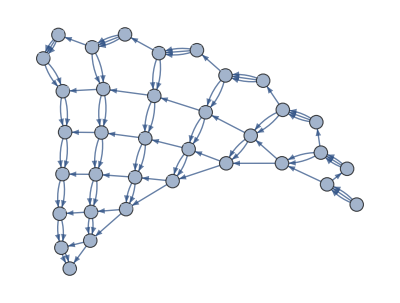
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss90=SSS[{"ABA"->"AAB","A"->"ABA"}, "A",75,SSSMax->25, NetMax->35,SSSSize->100,NetSize->400, VertexSize->0.6];
```

#### MaxStateLengthPositions: positions in "Evolution" where a new maximum state string length is reached for the first time

```mathematica
MaxStateLengthPositions[sss90]
```

{2,4,7,11,16,22,29,37,46,56}

Visually, these are the positions in the sessie (colored) image where the state string got longer.

```mathematica
CheckDimension@MaxStateLengthPositions[sss90]
```

{2D,{1,0,1},2
2
1,2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

Identified as (probably) 2-dimensional, pattern valid starting from position 2.  In the 0^th row, provided by MaxStateLengthPositions, we see rapid, increasing growth.  In the row of 1^st differences, growth is linear.  The 2^nd differences row is constant, and the 3^rd differences row would be all 0.  (This is reminiscent of taking derivatives of a quadratic (2^nd-degree) polynomial:  the first derivative is a linear function, the 2^nd is a constant, the 3^rd is zero.

#### LeastUsedRulePositions: positions where the least-used rule was used

```mathematica
LeastUsedRulePositions[sss90]
```

{1,3,6,10,15,21,28,36,45,55,66}

```mathematica
sss90["RulesUsed"]
```

{2,1,2,1,1,2,1,1,1,2,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1}

```mathematica
CheckDimension@LeastUsedRulePositions[sss90]
```

{2D,{1,0,1},1
2
1,1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 66
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

Again, the 2nd differences row is constant, indicating 2-d behavior.

#### DistanceLastPositions: a list containing, for each positive integer n, the position of the last node that is n steps from origin on the undirected graph of "Net".

```mathematica
CheckDimension@DistanceLastPositions[sss90]
```

{2D,{1,0,1},2
3
1,2 | 5 | 9 | 14 | 20 | 27 | 35 | 44 | 54 | 65
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

#### DistanceTally: number of nodes in the undirected graph of "Net" that are no more than 1, 2, 3, ... steps from origin. (SSSAnimate[sss, VertexLabels → "VertexWeight"] gives a related, helpful visualization for the directed graph.)

```mathematica
CheckDimension@DistanceTally[sss90]
```

{2D,{1,3,1},7
5
1,1 | 2 | 4 | 7 | 12 | 18 | 25 | 33 | 42 | 52 | 63
1 | 2 | 3 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
SSSAnimate[sss90,VertexLabels->"VertexWeight",NetSize->400]
```

#### GuessDimension: tries all 4 approximative tests, with appropriate checks, changes "Verdict" if appropriate.

```mathematica
GuessDimension[sss90]
```

{{2D,{1,0,1},2
2
1,2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2D,{1,0,1},1
2
1,1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 66
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2D,{1,0,1},2
3
1,2 | 5 | 9 | 14 | 20 | 27 | 35 | 44 | 54 | 65
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2D,{1,3,1},7
5
1,1 | 2 | 4 | 7 | 12 | 18 | 25 | 33 | 42 | 52 | 63
1 | 2 | 3 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 |  | }}

```mathematica
sss90["Verdict"]
```

2D

#### Other examples:

```mathematica
sss1a=SSS[{"A"->"",""->"A"},"",25,SSSSize->{50,200},NetSize->{400,300}, VertexSize->0.6];
sss1a["Verdict"]
```

```mathematica
CheckDimension@LeastUsedRulePositions[sss1a]
```

{1D,{1,0,2},2
2,2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
CheckDimension@MaxStateLengthPositions[sss1a]
```

{1D,{1,0,2},2
2,2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
CheckDimension@DistanceLastPositions[sss1a]
```

{failed,2
}

```mathematica
CheckDimension@DistanceTally[sss1a]
```

{failed,1
}

```mathematica
GuessDimension[sss1a]
```

Repeating

```mathematica
TestForUnusedRules[sss1a]
```

{}

If the sessie is disconnected, neither DistanceTally nor DistanceLastPositions may generate a usable list.  But fortunately, any repeating sessie can automatically be assumed to have dimension 1.   This is supported by all tests for repeating, connected cases.  So GuessDimension returns immediately in these cases.

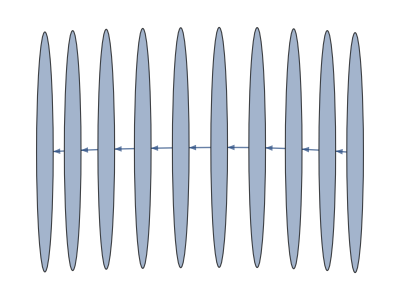
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

Repeating

Repeating

{}

```mathematica
sss1b=SSS[4,20,SSSSize->{50,200},Max->10,NetSize->{400,300}, VertexSize->0.6];
sss1b["Verdict"]
GuessDimension[sss1b]
TestForUnusedRules[sss1b]
```

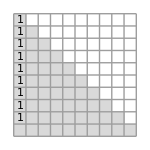
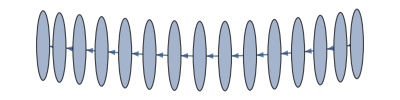
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

OK

{{1D,{1,0,1},2
1,2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | },{1D,{1,0,1},1
1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | },{1D,{1,0,1},2
1,2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | },{1D,{1,0,1},1
1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }}

1D

{}

```mathematica
sss20=SSS[20,20,SSSMax->10,SSSSize->{150,150},NetMax->15,NetSize->{400,100}, VertexSize->.8];
sss20["Verdict"]
GuessDimension[sss20]
sss20["Verdict"]
TestForUnusedRules[sss20]
```

Note that GuessDimension has changed the "Verdict" field of sss20.

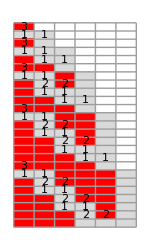



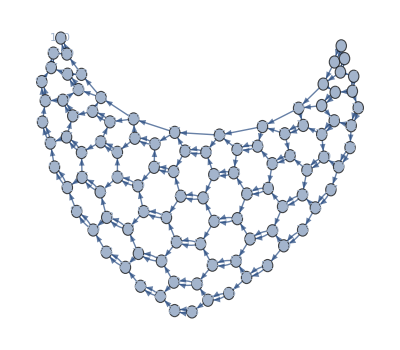
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

OK

{{2D,{1,0,2},7
5
2,7 | 12 | 19 | 28 | 39 | 52 | 67
5 | 7 | 9 | 11 | 13 | 15 | 
2 | 2 | 2 | 2 | 2 |  | },{2D,{1,0,2},6
5
2,6 | 11 | 18 | 27 | 38 | 51 | 66 | 83
5 | 7 | 9 | 11 | 13 | 15 | 17 | 
2 | 2 | 2 | 2 | 2 | 2 |  | },{2D,{1,0,2},5
5
2,5 | 10 | 17 | 26 | 37 | 50 | 65 | 82
5 | 7 | 9 | 11 | 13 | 15 | 17 | 
2 | 2 | 2 | 2 | 2 | 2 |  | },{2D,{3,0,4/3},1 | 2 | 4
1 | 2 | 3
1 | 1 | 2,1 | 2 | 4 | 7 | 12 | 18 | 25 | 34 | 44 | 55
1 | 2 | 3 | 5 | 6 | 7 | 9 | 10 | 11 | 
1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 |  | }}

2D

```mathematica
sssHex=SSS[{"AA"->"BA","AB"->"AA","B"->"AA"},"B",100,SSSMax->25,SSSSize->{150,250},NetMax->100,NetSize->{400,350}, VertexSize->1];
sssHex["Verdict"]
GuessDimension[sssHex]
sssHex["Verdict"]
```

```mathematica
TestForUnusedRules[sssHex]
```

{}

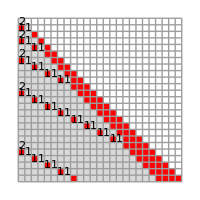
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

{{exp,{1,0,2},3
3
2,3 | 6 | 11 | 20 | 37 | 70 | 135 | 263
3 | 5 | 9 | 17 | 33 | 65 | 128 | 
2 | 4 | 8 | 16 | 32 | 63 |  | },{exp,{1,0,2},1
2
1,1 | 3 | 6 | 11 | 20 | 37 | 70 | 135 | 264
2 | 3 | 5 | 9 | 17 | 33 | 65 | 129 | 
1 | 2 | 4 | 8 | 16 | 32 | 64 |  | },{exp,{1,0,2},2
3
2,2 | 5 | 10 | 19 | 36 | 69 | 134
3 | 5 | 9 | 17 | 33 | 65 | 
2 | 4 | 8 | 16 | 32 |  | },{exp,{2,0,2},1 | 2
1 | 2
1 | 1,1 | 2 | 4 | 7 | 13 | 24 | 46 | 89
1 | 2 | 3 | 6 | 11 | 22 | 43 | 
1 | 1 | 3 | 5 | 11 | 21 |  | }}

exp

```mathematica
sssE=SSS[{"BA"->"AAB","A"->"BA"},"A",264,SSSMax->25,SSSSize->{200,200},NetSize->{400,300}, VertexLabels->None];
GuessDimension[sssE]
sssE["Verdict"]
```

```mathematica
TestForUnusedRules[sssE]
```

{}

If the sessie grows exponentially, growth positions are probably frequent and unimportant.  Only cross-checking with the rule used, done by the included MergeIntervalsByRulesUsed, permits limiting consideration to significant positions.

```mathematica
Length[sssE["Evolution"]]
```

265

CheckDimension identifies the network as exponential soon as the sequence of ratios appears.  FixedPointList would continue until lines have zero length:

```mathematica
FixedPointList[Differences,MaxStateLengthPositions[sssE]]//Column
```

{3,6,11,20,37,70,135,263}
{3,5,9,17,33,65,128}
{2,4,8,16,32,63}
{2,4,8,16,31}
{2,4,8,15}
{2,4,7}
{2,3}
{1}
{}
{}

Interestingly, here the exponential behavior was only found in the DistanceTally data when running averages of pairs of integers were summed, the raw data is harder to recognize:

```mathematica
FixedPointList[Differences,DistanceTally[sssE]]//Column
```

{1,2,4,7,13,24,46,89}
{1,2,3,6,11,22,43}
{1,1,3,5,11,21}
{0,2,2,6,10}
{2,0,4,4}
{-2,4,0}
{6,-4}
{-10}
{}
{}

```mathematica
MovingAverage[#,2]& /@ FixedPointList[Differences,DistanceTally[sssE]][[;;-4]]//Column
```

{3/2,3,11/2,10,37/2,35,135/2}
{3/2,5/2,9/2,17/2,33/2,65/2}
{1,2,4,8,16}
{1,2,4,8}
{1,2,4}
{1,2}
{1}

### Loop to display unique Sessies

<|Index→2,QCode→0,RuleSet→{A→,→A}|> : Repeating

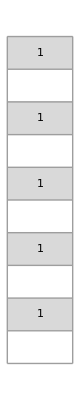
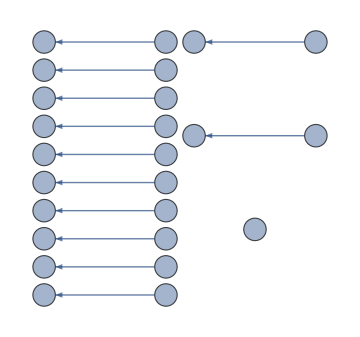
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→4,QCode→2,RuleSet→{A→A}|> : Repeating

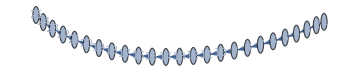
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→10,QCode→03,RuleSet→{A→,→AA}|> : Repeating

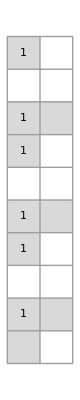
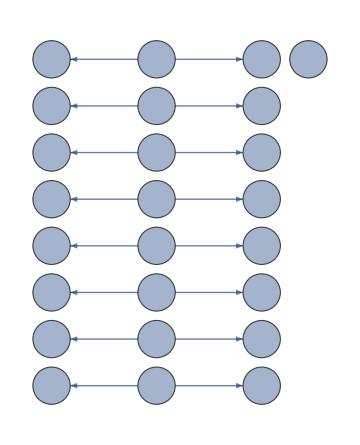
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→20,QCode→23,RuleSet→{A→AA}|> : 1D

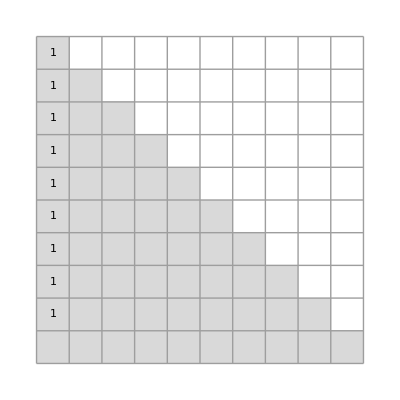
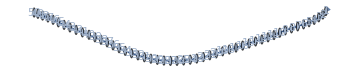
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→22,QCode→30,RuleSet→{AA→,→A}|> : Repeating

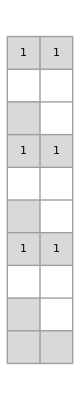
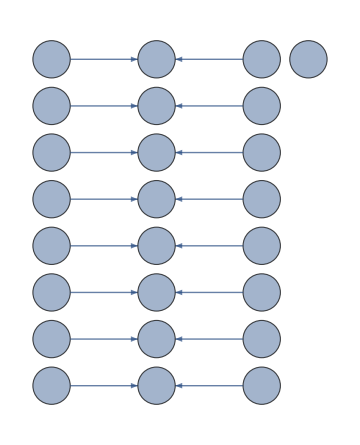
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50,QCode→033,RuleSet→{A→,→AAA}|> : Repeating

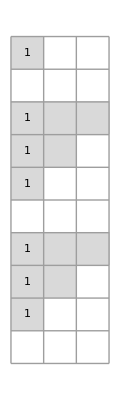
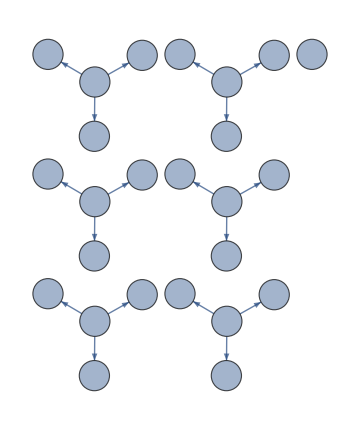
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→110,QCode→303,RuleSet→{AA→,→AA}|> : Repeating

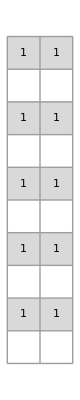
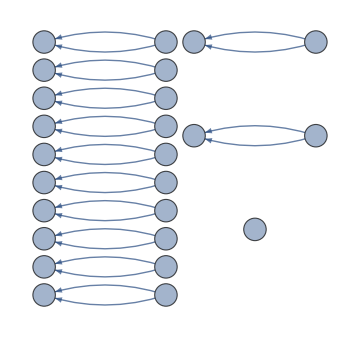
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→118,QCode→321,RuleSet→{AA→A,→A}|> : Repeating

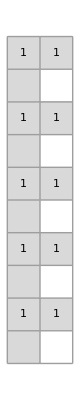
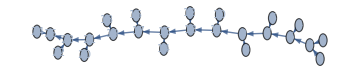
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→120,QCode→323,RuleSet→{AA→AA}|> : Repeating

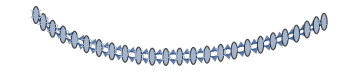
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→122,QCode→330,RuleSet→{AAA→,→A}|> : Repeating

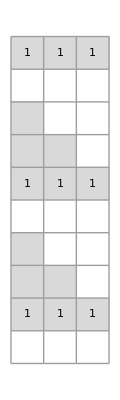
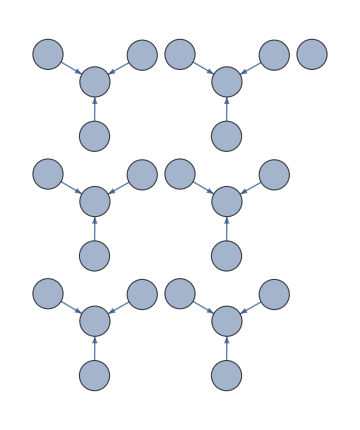
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

unreliable case: {A→,→AAAA}: {}

<|Index→250,QCode→0333,RuleSet→{A→,→AAAA}|> : Repeating

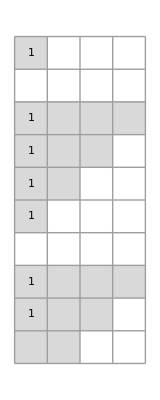
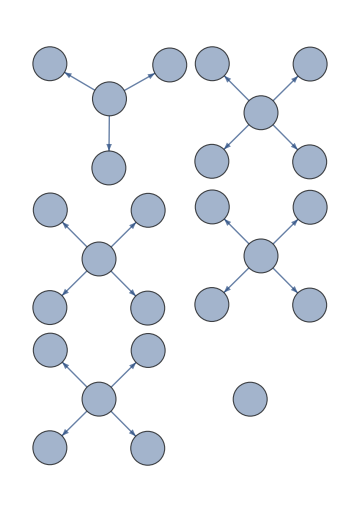
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→550,QCode→3033,RuleSet→{AA→,→AAA}|> : Repeating

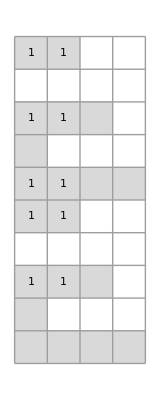
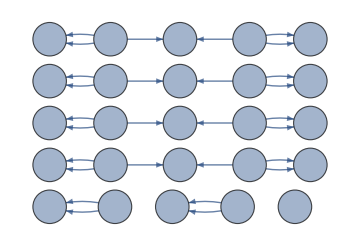
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→590,QCode→3213,RuleSet→{AA→A,→AA}|> : Repeating

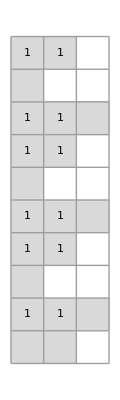
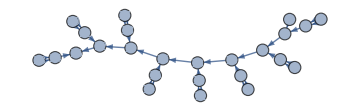
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→600,QCode→3233,RuleSet→{AA→AAA}|> : 1D

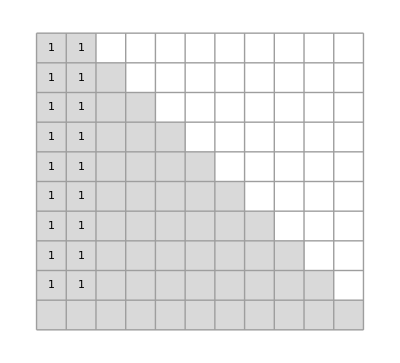
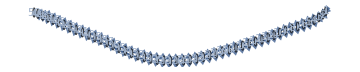
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→610,QCode→3303,RuleSet→{AAA→,→AA}|> : Repeating

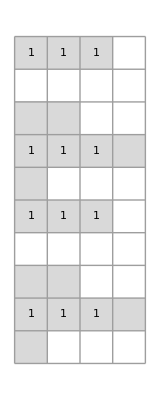
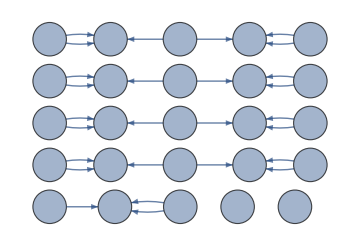
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→618,QCode→3321,RuleSet→{AAA→A,→A}|> : Repeating

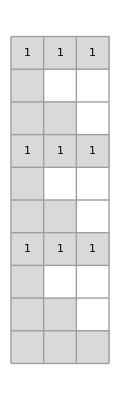
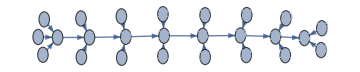
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

unreliable case: {AAAA→,→A}: {}

<|Index→622,QCode→3330,RuleSet→{AAAA→,→A}|> : Repeating

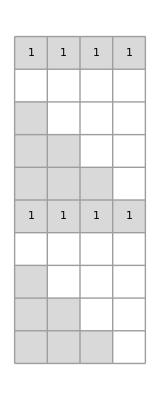
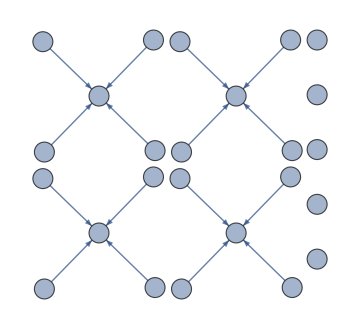
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

unreliable case: {A→,→AAAAA}: {}

<|Index→1250,QCode→03333,RuleSet→{A→,→AAAAA}|> : Repeating

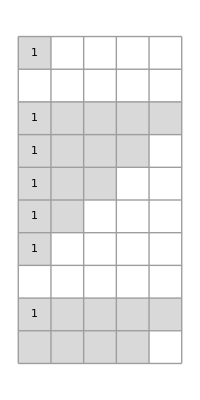
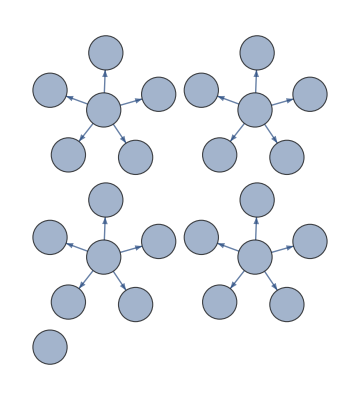
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1926,QCode→14034,RuleSet→{A→,B→,→AB}|> : Repeating

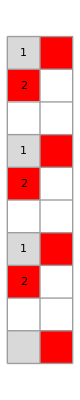
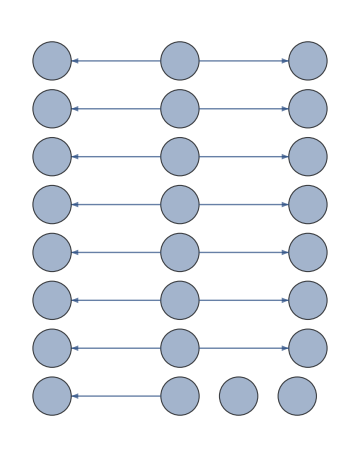
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1930,QCode→14043,RuleSet→{A→,B→,→BA}|> : Repeating

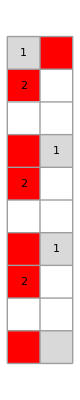
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1966,QCode→14214,RuleSet→{A→,B→A,→B}|> : Repeating

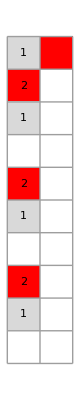
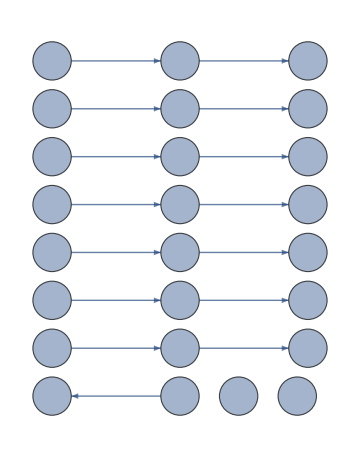
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1976,QCode→14234,RuleSet→{A→,B→AB}|> : Repeating

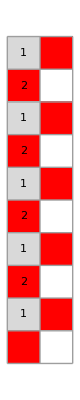
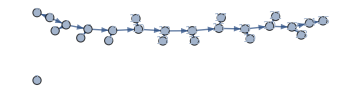
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1980,QCode→14243,RuleSet→{A→,B→BA}|> : Repeating

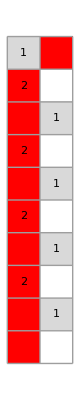
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2602,QCode→24240,RuleSet→{A→B,B→,→A}|> : Repeating

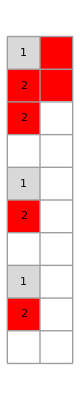
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2604,QCode→24242,RuleSet→{A→B,B→A}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2750,QCode→30333,RuleSet→{AA→,→AAAA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2800,QCode→31033,RuleSet→{AA→,A→,→AAA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2848,QCode→31231,RuleSet→{AA→,A→AA,→A}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2950,QCode→32133,RuleSet→{AA→A,→AAA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2960,QCode→32203,RuleSet→{AA→A,A→,→AA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2970,QCode→32223,RuleSet→{AA→A,A→AA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3050,QCode→33033,RuleSet→{AAA→,→AAA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3090,QCode→33213,RuleSet→{AAA→A,→AA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3098,QCode→33231,RuleSet→{AAA→AA,→A}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3100,QCode→33233,RuleSet→{AAA→AAA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→3110,QCode→33303,RuleSet→{AAAA→,→AA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3118,QCode→33321,RuleSet→{AAAA→A,→A}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

unreliable case: {AAAAA→,→A}: {}

<|Index→3122,QCode→33330,RuleSet→{AAAAA→,→A}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3176,QCode→34034,RuleSet→{AB→,→AB}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3180,QCode→34043,RuleSet→{AB→,→BA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3216,QCode→34214,RuleSet→{AB→A,→B}|> : OK

```mathematica
$debug=False;
rs=FromReducedRankIndex[1];               (* or other starting point in the enumeration *)
While[rs["Index"]<10^4,                         (* or some other large number, stopping point *)
(* Print[rs["Index"]]; *)
Which[
(Length[ans=TestForAll[rs]])>0,rs=ans; Continue[],  (* skip all possible *)

sss=SSS[rs["RuleSet"],25,Mode->Silent];  (* create the sessie for this ruleset *)
MatchQ[sss["Verdict"],"Dead"], (* do nothing! *) ,

GuessDimension[sss];
Length[ans=TestForUnusedRules[sss]]>0, rs=ans; Continue[], (* skip more! *)

True, (* else *)
Print[rs ," : ",sss⟦"Verdict"⟧];
Print@SSSDisplay[sss,SSSMax->10,SSSSize->Tiny,NetSize->Medium,VertexSize->0.8,VertexLabels->Placed[Automatic,Center]];
];
rs=FromReducedRankIndex[rs["Index"]+1]    (* increment *)
]
```

```mathematica
rs
```

<|Index→3216,QCode→34214,RuleSet→{AB→A,→B}|>

```mathematica
$debug=False;
```

```mathematica
sssT=SSS[3216,25];
```

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sssT["Verdict"]
```

OK

```mathematica
sssT["RulesUsed"]
```

{1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
TestForUnusedRules[sssT]
```

{}